```mathematica
Nx=15;
Ny=15;
nx=15;
ny=15;
```

```mathematica
coulombvaldatoccu={1.55,1.75,1.95,2,2.05,2.2,2.4,2.5,2.6,3,3.2,3.6};

datrotuwsoca=Table[Flatten[Import[StringJoin["Us1_",ToString[coulombval],"_nutcalca.dat"]]],{coulombval,coulombvaldatoccu}];
datrotdwsoca=Table[Flatten[Import[StringJoin["Us1_",ToString[coulombval],"_ndtcalca.dat"]]],{coulombval,coulombvaldatoccu}];
datrotuwsocb=Table[Flatten[Import[StringJoin["Us1_",ToString[coulombval],"_nutcalcb.dat"]]],{coulombval,coulombvaldatoccu}];
datrotdwsocb=Table[Flatten[Import[StringJoin["Us1_",ToString[coulombval],"_ndtcalcb.dat"]]],{coulombval,coulombvaldatoccu}];
```

```mathematica
occupationa=Table[Table[Partition[(datrotuwsoca[[l]]+datrotdwsoca[[l]]),3][[i,1]] + Partition[(datrotuwsoca[[l]]+datrotdwsoca[[l]]),3][[i,2]]+ Partition[(datrotuwsoca[[l]]+datrotdwsoca[[l]]),3][[i,3]],{i,1,Nx*Ny}][[1]],{l,1,Length[coulombvaldatoccu]}];


occupationb=Table[Table[Partition[(datrotuwsocb[[l]]+datrotdwsocb[[l]]),3][[i,1]] + Partition[(datrotuwsocb[[l]]+datrotdwsocb[[l]]),3][[i,2]]+ Partition[(datrotuwsocb[[l]]+datrotdwsocb[[l]]),3][[i,3]],{i,1,Nx*Ny}][[1]],{l,1,Length[coulombvaldatoccu]}];
```

```mathematica
occudata=Table[{coulombvaldatoccu[[i]],(occupationb-occupationa)[[i]]},{i,1,Length[coulombvaldatoccu]}];
crossingpt=8;
```

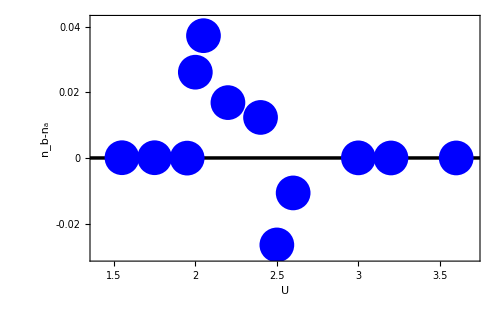

```mathematica
occuplot=ListPlot[occudata,Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.005],Black,32],Epilog->{{Blue,PointSize[0.05],Point[Take[occudata,crossingpt]]},
{Blue,PointSize[0.05],Point[Take[occudata,-(Length[occudata]-crossingpt)]]}},GridLines->{None,{0}},GridLinesStyle->Directive[Black,Thickness[0.005]],PlotRange->{{1.4,3.7},{-0.03,0.042}},
FrameTicks->{{{{-0.02,-0.02,0.03},{0,0,0.03},{0.02,0.02,0.03},{0.04,0.04,0.03}},{{-0.02,Null,0.03},{0,Null,0.03},{0.02,Null,0.03},{0.04,Null,0.03}}},{{{1.5,1.5,0.03},{2,2,0.03},{2.5,2.5,0.03},{3,3,0.03},{3.5,3.5,0.03}},{{1.5,Null,0.03},{2,Null,0.03},{2.5,Null,0.03},{3,Null,0.03},{3.5,Null,0.03}}}},
LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,25]},
FrameLabel->{{Style["n_b-n_a",35,FontFamily->"TimesNewRoman"],None},{Style["U",35,FontFamily->"TimesNewRoman"],None}},ImagePadding->{{125,15},{90,17}},ImageSize->500]
Export["occuplot.eps",occuplot];
```